# Learning Fourier Series in Mathematica

## April 24, 2019

Kirk Boyd
PHYS 300 - Walden

## Are these basis functions orthogonal? Are they orthonormal?

```mathematica
(*1*)(*a*)
```

```mathematica
un[x_]=E^(I*(n*Pi*x)/L)
```

ⅇ^(ⅈ n π x)

```mathematica
um[x_]=E^(I*(m*Pi*x)/L)
```

ⅇ^(ⅈ m π x)

```mathematica
Assuming[n∈Integers&&m∈Integers&&L>0,∫_-L^L Conjugate[un[x]]*um[x]ⅆx]
```

0

```mathematica
Assuming[n∈Integers&&m∈Integers&&L>0,∫_-L^L Conjugate[um[x]]*un[x]ⅆx]
```

0

```mathematica
(*b*)
Assuming[n∈Integers&&L>0&&n==m,∫_-L^L Conjugate[un[x]]*um[x]ⅆx]
```

2

```mathematica
(*c*)
```

```mathematica
(*2*)
n's to include: all integers
```

```mathematica
(*3*)
```

```mathematica
Assuming[L>0,f[x_]=Abs[Sin[(Pi*x)/(2L)]]]
```

Abs[Sin[(π x)/2]]

```mathematica
(*4*)
```

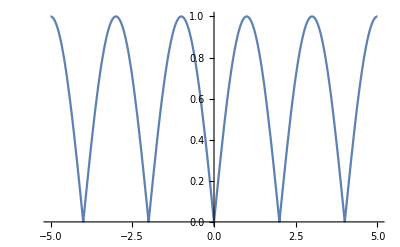

```mathematica
L=1;
Plot[f[x],{x,-5L,5L}]
```

```mathematica
(*5*)
```

```mathematica
Assuming[n∈Integers,c[n_]=((∫_-L^L un[x]*f[x]ⅆx)/2L)]
```

-2/((-1+4 n^2) π)

```mathematica
(*6*)
```

```mathematica
c[0]
```

2/π

```mathematica
c[1]
```

-2/(3 π)

```mathematica
c[2]
```

-2/(15 π)

```mathematica
c[-1]
```

-2/(3 π)

```mathematica
c[100]
```

-2/(39999 π)

```mathematica
(*7*)
```

```mathematica
(*8*)
```

```mathematica
fser[N_]:=Sum[c[n]un[x],{n,-N,N}]
```

```mathematica
fser[0]
```

c[0]

```mathematica
fser[1]
```

2/π-(2 ⅇ^(-ⅈ π x))/(3 π)-(2 ⅇ^(ⅈ π x))/(3 π)

```mathematica
(*9*)
```

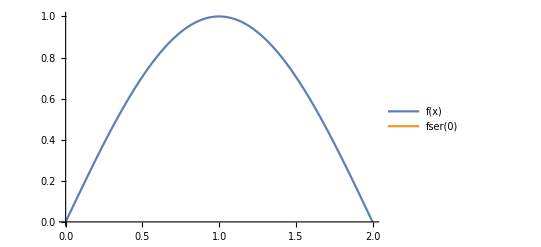

```mathematica
Plot[{f[x],fser[0]},{x,0,2L},PlotLegends->"Expressions"]
```

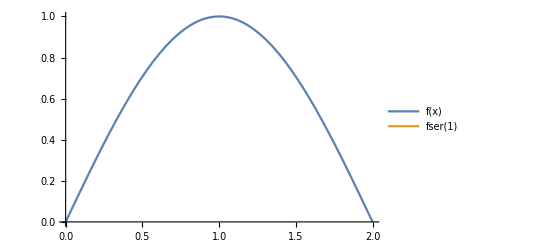

```mathematica
Plot[{f[x],fser[1]},{x,0,2L},PlotLegends->"Expressions"]
```

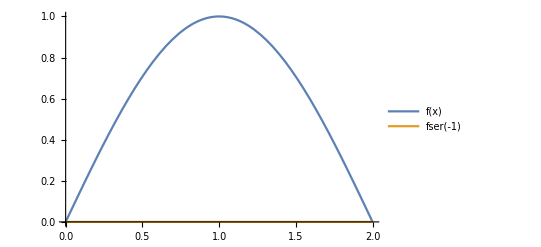

```mathematica
Plot[{f[x],fser[-1]},{x,0,2L},PlotLegends->"Expressions"]
```

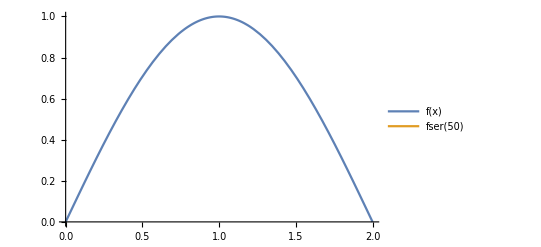

```mathematica
Plot[{f[x],fser[50]},{x,0,2L},PlotLegends->"Expressions"]
```